## System

### A 2D hexagonal lattice, of size [nmax × nmax × 2], with onsite Anderson disorder of strength u. Periodic boundary conditions.

```mathematica
Clear[H0,δH,H];  
nmax=400;
H0=With[{k={1,-1}0},(#+#†)&@ArrayFlatten@ArrayFlatten@SparseArray[
Flatten@Table[{If[i==nmax,{1,i, j,j,1,2}->1. ⅇ^(ⅈ k[[1]]),{i+1,i, j,j,1,2}->1.],If[j==nmax,{i,i, 1,j,1,2}->1. ⅇ^(ⅈ k[[2]]),{i,i,j+1,j,1,2}->1.],{i,i,j,j,1,2}->1.},{i,1,nmax},{j,1,nmax}],{nmax,nmax,nmax,nmax,2,2}]];
δH=SparseArray[{i_,i_}:>RandomReal[{-1,1}],{2 nmax^2,2 nmax^2}]
H[u_]:=H0+u δH
vx=(#+#†)&@ArrayFlatten@ArrayFlatten@SparseArray[
Flatten@Table[{If[i==nmax,{1,i, j,j,1,2}->ⅈ(√3.)/2,{i+1,i, j,j,1,2}->ⅈ(√3.)/2],If[j==nmax,{i,i, 1,j,1,2}->-ⅈ(√3.)/2,{i,i,j+1,j,1,2}->-ⅈ(√3.)/2],{i,i,j,j,1,2}->0.},{i,1,nmax},{j,1,nmax}],{nmax,nmax,nmax,nmax,2,2}];
```

SparseArray[<320000>,{320000,320000}]

#### Analytic DOS

From Yuan et al, Phys. Rev. B 82, 115448 (2010)

```mathematica
AnalyticDOS[ϵt_]:=Module[{F=(1+Abs@ϵt)^2-((ϵt^2-1)^2)/4},
Piecewise[{{(2Abs@ϵt)/π^2 1/(√F)EllipticK[(4 Abs@ϵt)/F],Abs@ϵt≤1},{(2Abs@ϵt)/π^2 1/(√(4Abs@ϵt))EllipticK[F/(4 Abs@ϵt)], 1<Abs@ϵt≤3}},0]]
```

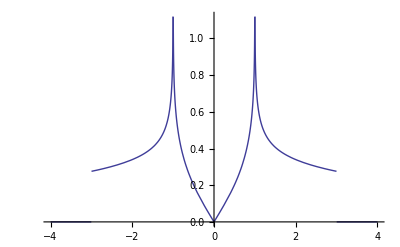

```mathematica
Plot[AnalyticDOS[ϵt],{ϵt,-4,4}]
```

#### What is the optimal sampling for a Chebyshev expansion of order N? Answer: ϵ_m=Cos[ϕ_m], with ϕ_m=π(m-1/2)/(N+1), m=1...N+1 (i.e. the zeroes of T_(N+1))

Without an upper cutoff for the Chebyshev expansion, we resolve a proper Dirac delta function
	δ(ϵ-ϵ’)=∑_n^∞ 1/ν_n N(ϵ) T_n(ϵ)T_n(ϵ'), 
If we truncate the sum, can we expect to still have a delta function if we constrain ϵ to a certain mesh? Yes, like in a Fourier transform→Fourier series.
To find the mesh, we use T_n(Cos[ϕ])=Cos[n ϕ], and the zeroes of T_(N+1)(ϵ) are ϵ_m=Cos[ϕ_m], with ϕ_m=π(m+1/2)/(N+1), m=1 ... N+1.
Then, using the identity
	2/(N+1) ∑_(n=0)^N 1/ν_n Cos[n ϕ_m]Cos[n ϕ_m']=δ_mm' for m=1.. N+1.
we can write
	2/(N+1) ∑_(n=0)^N 1/ν_n T_n[ϵ_sm]T_n[ϵ_s'm']=δ_(ϵ_m-ϵ_m')
The above is a Kronecker delta, instead of a Dirac Delta. Note the absence of N(ϵ) in the expression above. To get a Dirac delta again, we weight by the inverse of
dϵ_m=|ϵ_(m+1)-ϵ_m| =2Sin[π/(2(N+1))] Sin[(m π)/(N+1)] ≈ π/(N+1)√(1-ϵ_m^2)+O(N^-2). This gives, for large N, what we knew.
	1/dϵ_m2/(N+1) ∑_(n=0)^N 1/ν_n T_n[ϵ_sm]T_n[ϵ_s'm']≈∑_(n=0)^N 1/ν_n N(ϵ_m)T_n[ϵ_sm]T_n[ϵ_s'm']≈δ(ϵ_m-ϵ_m')
The code below demonstrates the δ_(ϵ_m-ϵ_m') relation

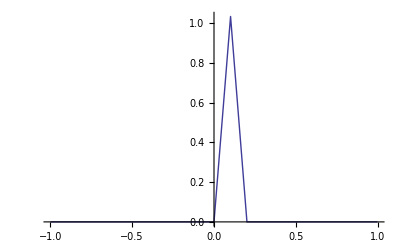

```mathematica
Clear@ChebyVecBare;
ChebyVecBare=Compile[{{ϵ,_Real},{nmax,_Integer}},Prepend[Last/@NestList[{#[[2]],2ϵ #[[2]]-#[[1]]}&,{1,ϵ},nmax-1],1],CompilationTarget->"C", RuntimeAttributes->{Listable}];
ϵmesh[m_,NN_]=Sign[m]Cos[π(m-0.5)/(NN+1)];
ϵmesh[NN_]:=Sort@ϵmesh[Range[1,NN+1],NN]
δKCh[m_Integer,mp_Integer,NN_Integer]:=Module[{ϵ=ϵmesh[m,NN],ϵp=ϵmesh[mp,NN],ch1,ch2},ch1=ChebyVecBare[ϵ,NN];ch2=ChebyVecBare[ϵp,NN]; ch1[[1]]*=.5;2/NN ch1.ch2 ]
Sort@With[{NN=30,m=15},{ϵmesh[#,NN],δKCh[#,m,NN]}&/@Range[1,NN+1]];
ListLinePlot[%, PlotRange->All]
```

```mathematica
ϵmesh[4]
ChebyshevT[5,ϵmesh[4]]
```

{-0.951057,-0.587785,6.12323×10^-17,0.587785,0.951057}

{6.66134×10^-16,-6.66134×10^-16,3.06162×10^-16,1.11022×10^-16,-6.66134×10^-16}

There is an important problem with this sampling however: it only gives a clean resolution of δ(ϵ-ϵ’) when both ϵ and ϵ’ are points in the mesh. In the case of δ(ϵ_m-h), the eigenvalues of h are not in the mesh, and the resolution is no cleaner than a random mesh in this case (except at those points in which eigenvalues of h fall in the mesh, of course). See code below.

```mathematica
Clear@ChebyVecBare;
ChebyVecBare=Compile[{{ϵ,_Real},{nmax,_Integer}},Prepend[Last/@NestList[{#[[2]],2ϵ #[[2]]-#[[1]]}&,{1,ϵ},nmax-1],1],CompilationTarget->"C", RuntimeAttributes->{Listable}];
(*ϵmesh[m_,NN_]=Sign[m]Cos[π(m-0.5)/(NN+1)];*)
ϵmesh0[NN_]:=Sort@Range[-1,1,1/Round[NN/π]]
ϵmesh[m_,NN_]=Sign[m]Cos[π(m-0.5)/(NN+1)];
ϵmesh[NN_]:=Sort@ϵmesh[Range[1,NN+1],NN]
δKCh[ϵ_,ϵp_,NN_Integer]:=Module[{ch1,ch2},ch1=ChebyVecBare[ϵ,NN];ch2=ChebyVecBare[ϵp,NN]; ch1[[1]]*=.5;2/NN ch1.ch2 ]
Manipulate[ListLinePlot[#,PlotRange->All]&@Sort@With[{NN=30},{{ϵmesh[NN],δKCh[#,ϵp,NN]&/@ϵmesh[NN]}ᵀ,{ϵmesh0[NN],δKCh[#,ϵp,NN]&/@ϵmesh0[NN]}ᵀ}],{{ϵp,0},-1,1}]
```

Nevertheless, using this sampling gives a clean F(ϵ_m,ϵ_m'), while any other sampling has artifacts. This is the F(ϵ_m,ϵ_m') with a proper mesh

-Graphics-

... while this is the same with a uniform mesh

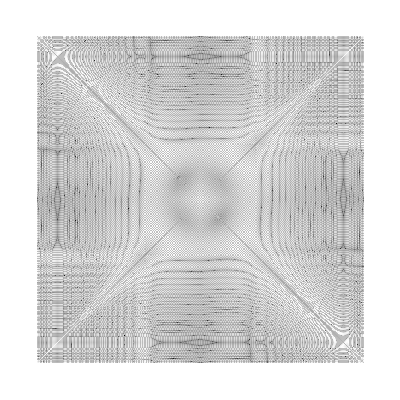

-Graphics-

The extra beating oscillating sign can be filtered out by a simple convolution

```mathematica
KuboσF[Mean[tempK600], InterpolationOrder->0];
Manipulate[ListLinePlot[{Diagonal[#,200],Diagonal[#,201]}, PlotRange->{-1,1}z]&@ListCorrelate[1/(γ+4(α+β))({{β/4, α/4, β/4}, {α/4, γ, α/4}, {β/4, α/4, β/4}}),temp],{{α,1},0,3},{{β,0},-3,3},{{γ,1},0,3},{z,0,.01}]
(*ArrayPlot[Log@%%]*)
```

#### Tests

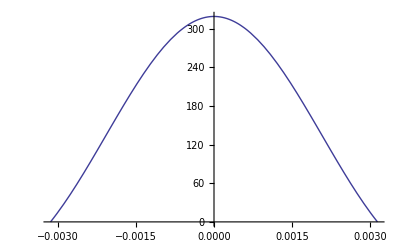

```mathematica
Clear@ChebyVec;
ChebyVec=Compile[{{ϵ,_Real},{nmax,_Integer}},2./(π √(1-ϵ^2))Prepend[Last/@NestList[{#[[2]],2ϵ #[[2]]-#[[1]]}&,{1,ϵ},nmax-1],1],CompilationTarget->"C", RuntimeAttributes->{Listable}];
Clear@δCh;
δCh[ϵ_?NumericQ,n_Integer]:=ChebyVec[ϵ,n].ChebyVec[0,n] π/2
δW[n_Integer]:=√NIntegrate[δCh[ϵ,n] ϵ^2,{ϵ,-.999,.999}, MaxRecursion->60]
With[{n=1000},Plot[δCh[ϵ,n],{ϵ,-π/n,π/n}, PlotRange->All]]
```

```mathematica
Cos[π(Range[3])/3]
```

{1/2,-1/2,-1}

```mathematica
With[{n=10},ChebyVec[#,n]&/@Cos[π(Range[n]-1/2)/n]]
With[{n=10.},Cos[π(Range[n])/n]]
```

{{4.06956,4.01946,3.87038,3.62601,3.29234,2.87761,2.39203,1.84754,1.25756,0.63662,9.03624×10^-15},{1.40228,1.24944,0.824237,0.219364,-0.433327,-0.991559,-1.33364,-1.38501,-1.13446,-0.63662,-1.08979×10^-15},{0.900316,0.63662,-1.9991×10^-16,-0.63662,-0.900316,-0.63662,5.99731×10^-16,0.63662,0.900316,0.63662,-8.99597×10^-16},{0.714495,0.324374,-0.41997,-0.705698,-0.220791,0.505224,0.679525,0.111772,-0.578039,-0.63662,3.173×10^-16},{0.644555,0.100831,-0.613009,-0.292622,0.521456,0.455769,-0.37886,-0.574303,0.199179,0.63662,-3.578×10^-17},{0.644555,-0.100831,-0.613009,0.292622,0.521456,-0.455769,-0.37886,0.574303,0.199179,-0.63662,-3.578×10^-17},{0.714495,-0.324374,-0.41997,0.705698,-0.220791,-0.505224,0.679525,-0.111772,-0.578039,0.63662,3.173×10^-16},{0.900316,-0.63662,-1.9991×10^-16,0.63662,-0.900316,0.63662,5.99731×10^-16,-0.63662,0.900316,-0.63662,-8.99597×10^-16},{1.40228,-1.24944,0.824237,-0.219364,-0.433327,0.991559,-1.33364,1.38501,-1.13446,0.63662,-1.08979×10^-15},{4.06956,-4.01946,3.87038,-3.62601,3.29234,-2.87761,2.39203,-1.84754,1.25756,-0.63662,9.03624×10^-15}}

{0.951057,0.809017,0.587785,0.309017,6.12323×10^-17,-0.309017,-0.587785,-0.809017,-0.951057,-1.}

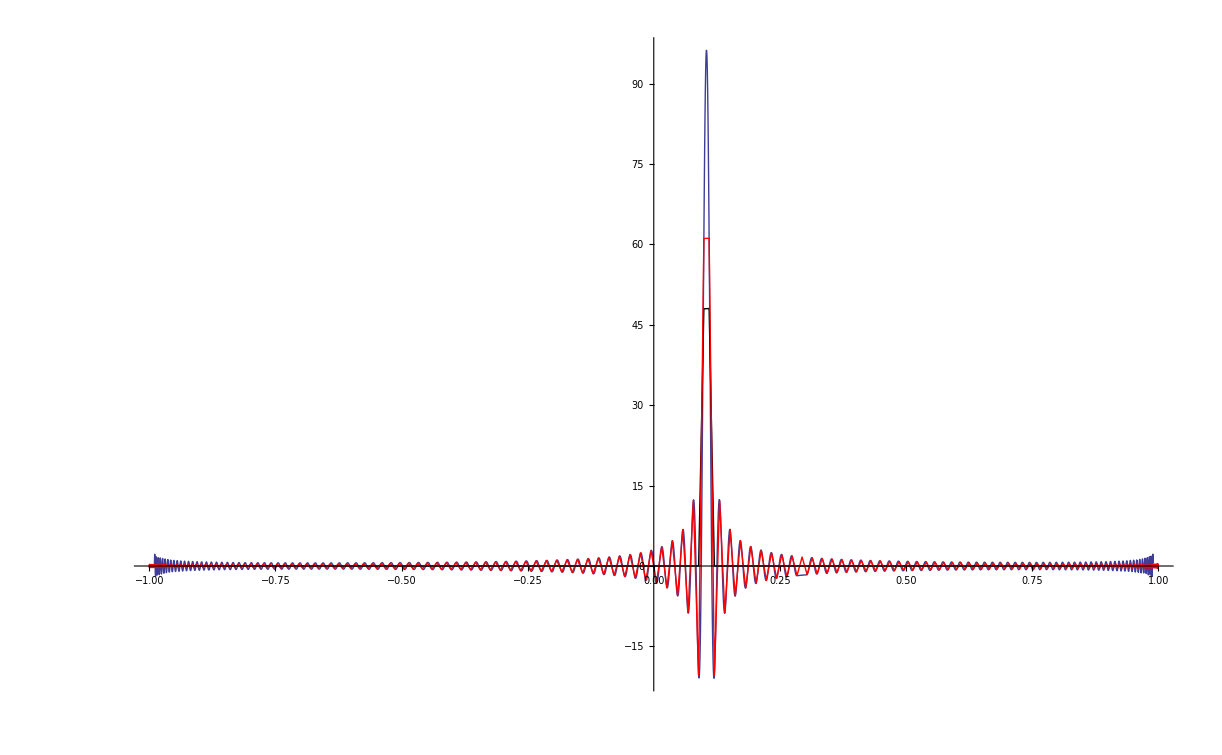

```mathematica
Clear@δCh2;
δCh2[ϵ_?NumericQ,n_Integer,m_Integer]:=Module[{ch1=ChebyVec[ϵ,n],ϵp=Cos[π(m/2-.5)/n],ch2},ch2=ChebyVec[ϵp,n]; ch1[[1]]*=.5;ch1.ch2 (2/(π √(1-ϵp^2)))^-1]
With[{n=300, m=281},Plot[δCh2[ϵ,n,m],{ϵ,-.99,.99}, PlotRange->All, Epilog->{Line[{#,(δCh2[#,n,m-1]+δCh2[#,n,m+1])/2}&/@Cos[π(Range[n]-.5)/n]],Red,Line[{#,δCh2[#,n,m]}&/@Cos[π(Range[n]-.5)/n]]}]]
```

```mathematica
NIntegrate[δCh2[ϵ,300,280],{ϵ,-1,1}]
```

1.

0.999982

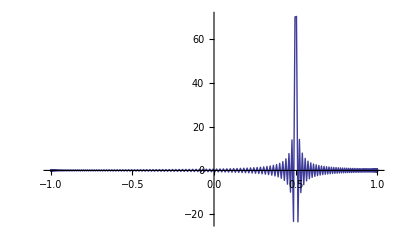

```mathematica
With[{n=300,m=201},{#,δCh2[#,n,m]}&/@Cos[π(Range[n]-.5)/n]];
Total@Table[(%[[n,1]]-%[[n+1,1]])(%[[n+1,2]]+%[[n,2]])/2,{n,1,Length[%]-1}]
ListLinePlot[%%,PlotRange->All]
```

0.999982

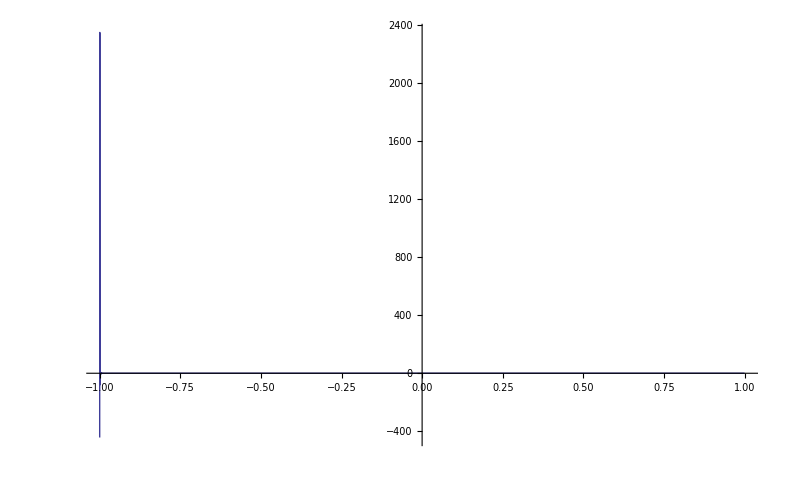

```mathematica
δCh2[ϵ_?NumericQ,n_Integer,m_Integer]:=Module[{ch1=ChebyVec[ϵ,n],ϵp=Sign[m]Cos[π(m/2-.5)/n],ch2},ch2=ChebyVec[ϵp,n]; ch1[[1]]*=.5;ch1.ch2 (2/(π √(1-ϵp^2)))^-1]
With[{n=300,m=-4},{#,(δCh2[#,n,m-1]+δCh2[#,n,m+1])/2}&/@Cos[π(Range[1,n]-.5)/n]];
Total@Table[(%[[n,1]]-%[[n+1,1]])(%[[n+1,2]]+%[[n,2]])/2,{n,1,Length[%]-1}]
ListLinePlot[%%,PlotRange->All]
```

Part::pspec: Part specification n is neither a machine-sized integer nor a list of machine-sized integers.

Part::pspec: Part specification 1 + n is neither a machine-sized integer nor a list of machine-sized integers.

General::stop: Further output of Part :: pspec will be suppressed during this calculation.

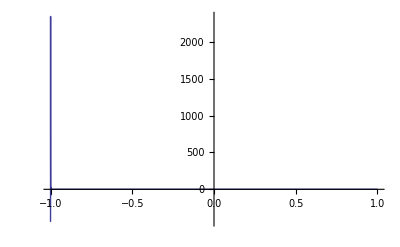
(-Graphics-)⟦n,1⟧-(-Graphics-)⟦1+n,1⟧

```mathematica
(%[[n,1]]-%[[n+1,1]])
```

```mathematica
FullSimplify[Cos[π(m-1/2)/n]-Cos[π(m+1-1/2)/n]]
```

2 Sin[π/(2 n)] Sin[(m π)/n]

{1.00632,0.983632,0.983632}

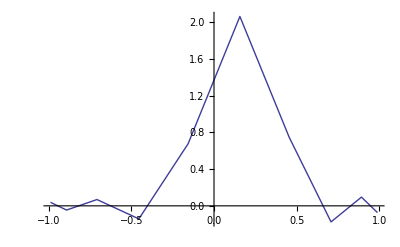

```mathematica
δCh2[ϵ_?NumericQ,n_Integer,m_Integer]:=Module[{ch1=ChebyVec[ϵ,n],ϵp=Sign[m]Cos[π(m/2-.5)/n],ch2},ch2=ChebyVec[ϵp,n]; ch1[[1]]*=.5;ch1.ch2 (2/(π √(1-ϵp^2)))^-1]
With[{n=10,m=-90},{#,(δCh2[#,n,m-1]+δCh2[#,n,m+1])/2}&/@Cos[π(Range[1,n]-.5)/n]];
With[{NN=10},{
Total@Table[2 Sin[π/(2 NN)] Sin[(m π)/NN]%[[m,2]],{m,1,NN}],
Total@Table[2 Sin[π/(2 NN)] Sin[(m π)/NN](%[[m+1,2]]+%[[m,2]])/2,{m,1,NN-1}],
Total@Table[2 Sin[π/(2 NN)] Sin[(m π)/NN](%[[m+1,2]]+%[[m,2]])/2,{m,1,NN-1}]}]
ListLinePlot[%%,PlotRange->All]
```

```mathematica
Sign[1]Cos[π(1/2-.5)/100]
```

1.

2 Sin[π/(2 NN)] √(Sin[(π Abs[m])/NN] Sin[(π Abs[mp])/NN])

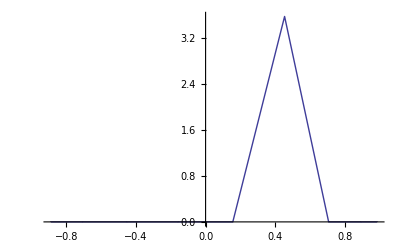

```mathematica
Clear@ChebyVecBare;
ChebyVecBare=Compile[{{ϵ,_Real},{nmax,_Integer}},Prepend[Last/@NestList[{#[[2]],2ϵ #[[2]]-#[[1]]}&,{1,ϵ},nmax-1],1],CompilationTarget->"C", RuntimeAttributes->{Listable}];
ϵmesh[m_,NN_]=Sign[m]Cos[π(m-.5)/NN];
δKCh[m_Integer,mp_Integer,NN_Integer]:=Module[{ϵ=ϵmesh[m,NN],ϵ2=ϵmesh[m+1,NN],ϵp=ϵmesh[mp,NN],ϵp2=ϵmesh[mp+1,NN],ch1,ch2},ch1=(ChebyVecBare[ϵ,NN]+ChebyVecBare[ϵ2,NN])/2;ch2=(ChebyVecBare[ϵp,NN]+ChebyVecBare[ϵp2,NN])/2; ch1[[1]]*=.5;ch1.ch2 (2/(π √(1-ϵp^2)))]
δKCh[m_Integer,mp_Integer,NN_Integer]:=Module[{ϵ=ϵmesh[m,NN],ϵp=ϵmesh[mp,NN],ch1,ch2},ch1=ChebyVecBare[ϵ,NN];ch2=ChebyVecBare[ϵp,NN]; ch1[[1]]*=.5;ch1.ch2 √((2/(π √(1-ϵp^2)))(2/(π √(1-ϵ^2))))]
Δ[m_Integer,mp_Integer,NN_Integer]=2Sin[π/(2NN)] √(Sin[(Abs[m] π)/NN]Sin[(Abs[mp] π)/NN])
With[{NN=10,m=-6},{ϵmesh[#,NN],δKCh[#,m,NN]}&/@Join[Range[-NN+1,-1],Range[1,NN-1]]];
ListLinePlot[Sort@%, PlotRange->All]
```

```mathematica
ChebyshevT[6,-Cos[2.]]/Cos[6 2.]
```

1.

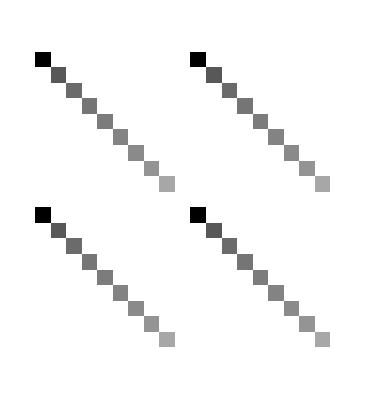

```mathematica
With[{NN=10},Table[Δ[m,mp,NN]δKCh[m,mp,NN],{m,-NN,NN},{mp,-NN+1,NN}]]//ArrayPlot
```

```mathematica
.
```

```mathematica
With[{NN=100,m=81},{ϵmesh[#,NN],DD[m,#,NN]}&/@Range[-NN,NN]];
ListLinePlot[%,PlotRange->All]
```

-Graphics-

```mathematica
With[{NN=300},ChebyshevT[NN,#]&/@Cos[π(Range[1,NN]-.5)/NN]]//Chop
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

We will use a discrete, non-uniform ϵ mesh for F(ϵ,ϵ’). We will take ϵ_m=Sign[m]Cos[π(m-1/2)/N], with |m|=1...N, i.e. the zeroes of the N-th Cheby polynomial, T_N(ϵ_m)=0. In this way, the continuous projector identity
	δ(ϵ-ϵ’)=∑_n 1/ν_n N(ϵ) T_n(ϵ)T_n(ϵ'), 
turns into
	D_(m,m')= ∑_n 1/ν_n N(ϵ_m) T_n(ϵ_m)T_n(ϵ_m')=δ(ϵ_m-ϵ_m').
This is still a Dirac delta function, in the sense that ∫ dϵ δ(ϵ-ϵ_m')=1. However, using the above mesh, we also have a discrete Kronecker delta
	∑_m 2 Sin[π/(2 n)] Sin[(m π)/n]D_(m+1,m)=1
We can, however, turn this int

#### Tests

```mathematica
Sort@With[{n=100},{#,δCh2[#,n]}&/@Most@Cos[π(Range[n]-.5)/n]];
With[{NN=100},Total@Table[2./(π √(1-Cos[π(n-.5)/NN]^2))δCh2[Cos[π(n-.5)/NN],NN],{n,0,NN-1}]]
```

13.5145 δCh2[-0.99889,100]+8.11403 δCh2[-0.996917,100]+5.80147 δCh2[-0.993961,100]+4.5182 δCh2[-0.990024,100]+3.7028 δCh2[-0.985109,100]+3.13935 δCh2[-0.979223,100]+2.72706 δCh2[-0.97237,100]+2.4126 δCh2[-0.964557,100]+2.16508 δCh2[-0.955793,100]+1.96538 δCh2[-0.946085,100]+1.80103 δCh2[-0.935444,100]+1.66357 δCh2[-0.92388,100]+1.54702 δCh2[-0.911403,100]+1.44706 δCh2[-0.898028,100]+1.3605 δCh2[-0.883766,100]+1.28491 δCh2[-0.868632,100]+1.21841 δCh2[-0.85264,100]+1.15955 δCh2[-0.835807,100]+1.10715 δCh2[-0.81815,100]+1.06029 δCh2[-0.799685,100]+1.0182 δCh2[-0.78043,100]+0.980247 δCh2[-0.760406,100]+0.945926 δCh2[-0.739631,100]+0.914798 δCh2[-0.718126,100]+0.886501 δCh2[-0.695913,100]+0.860726 δCh2[-0.673013,100]+0.83721 δCh2[-0.649448,100]+0.815729 δCh2[-0.625243,100]+0.796089 δCh2[-0.60042,100]+0.778121 δCh2[-0.575005,100]+0.761682 δCh2[-0.549023,100]+0.746645 δCh2[-0.522499,100]+0.7329 δCh2[-0.495459,100]+0.720349 δCh2[-0.46793,100]+0.708909 δCh2[-0.439939,100]+0.698505 δCh2[-0.411514,100]+0.689072 δCh2[-0.382683,100]+0.680554 δCh2[-0.353475,100]+0.672899 δCh2[-0.323917,100]+0.666064 δCh2[-0.29404,100]+0.660012 δCh2[-0.263873,100]+0.654709 δCh2[-0.233445,100]+0.650128 δCh2[-0.202787,100]+0.646243 δCh2[-0.171929,100]+0.643035 δCh2[-0.140901,100]+0.640488 δCh2[-0.109734,100]+0.638588 δCh2[-0.0784591,100]+0.637327 δCh2[-0.0471065,100]+0.636698 δCh2[-0.0157073,100]+0.636698 δCh2[0.0157073,100]+0.637327 δCh2[0.0471065,100]+0.638588 δCh2[0.0784591,100]+0.640488 δCh2[0.109734,100]+0.643035 δCh2[0.140901,100]+0.646243 δCh2[0.171929,100]+0.650128 δCh2[0.202787,100]+0.654709 δCh2[0.233445,100]+0.660012 δCh2[0.263873,100]+0.666064 δCh2[0.29404,100]+0.672899 δCh2[0.323917,100]+0.680554 δCh2[0.353475,100]+0.689072 δCh2[0.382683,100]+0.698505 δCh2[0.411514,100]+0.708909 δCh2[0.439939,100]+0.720349 δCh2[0.46793,100]+0.7329 δCh2[0.495459,100]+0.746645 δCh2[0.522499,100]+0.761682 δCh2[0.549023,100]+0.778121 δCh2[0.575005,100]+0.796089 δCh2[0.60042,100]+0.815729 δCh2[0.625243,100]+0.83721 δCh2[0.649448,100]+0.860726 δCh2[0.673013,100]+0.886501 δCh2[0.695913,100]+0.914798 δCh2[0.718126,100]+0.945926 δCh2[0.739631,100]+0.980247 δCh2[0.760406,100]+1.0182 δCh2[0.78043,100]+1.06029 δCh2[0.799685,100]+1.10715 δCh2[0.81815,100]+1.15955 δCh2[0.835807,100]+1.21841 δCh2[0.85264,100]+1.28491 δCh2[0.868632,100]+1.3605 δCh2[0.883766,100]+1.44706 δCh2[0.898028,100]+1.54702 δCh2[0.911403,100]+1.66357 δCh2[0.92388,100]+1.80103 δCh2[0.935444,100]+1.96538 δCh2[0.946085,100]+2.16508 δCh2[0.955793,100]+2.4126 δCh2[0.964557,100]+2.72706 δCh2[0.97237,100]+3.13935 δCh2[0.979223,100]+3.7028 δCh2[0.985109,100]+4.5182 δCh2[0.990024,100]+5.80147 δCh2[0.993961,100]+8.11403 δCh2[0.996917,100]+13.5145 δCh2[0.99889,100]+81.0603 δCh2[0.999877,100]

```mathematica
Sort@With[{n=100},{#,δCh2[#,n]}&/@Most@Cos[π(Range[n]-.5)/n]];
Times@@#&/@({Differences[%ᵀ[[1]]],MovingAverage[%ᵀ[[2]],2]}ᵀ);
Total@%
```

0.000986271 (δCh2[-0.99889,100]+δCh2[-0.996917,100])+0.00147819 (δCh2[-0.996917,100]+δCh2[-0.993961,100])+0.00196865 (δCh2[-0.993961,100]+δCh2[-0.990024,100])+0.00245717 (δCh2[-0.990024,100]+δCh2[-0.985109,100])+0.00294326 (δCh2[-0.985109,100]+δCh2[-0.979223,100])+0.00342645 (δCh2[-0.979223,100]+δCh2[-0.97237,100])+0.00390625 (δCh2[-0.97237,100]+δCh2[-0.964557,100])+0.0043822 (δCh2[-0.964557,100]+δCh2[-0.955793,100])+0.00485383 (δCh2[-0.955793,100]+δCh2[-0.946085,100])+0.00532066 (δCh2[-0.946085,100]+δCh2[-0.935444,100])+0.00578225 (δCh2[-0.935444,100]+δCh2[-0.92388,100])+0.00623813 (δCh2[-0.92388,100]+δCh2[-0.911403,100])+0.00668785 (δCh2[-0.911403,100]+δCh2[-0.898028,100])+0.00713097 (δCh2[-0.898028,100]+δCh2[-0.883766,100])+0.00756706 (δCh2[-0.883766,100]+δCh2[-0.868632,100])+0.00799568 (δCh2[-0.868632,100]+δCh2[-0.85264,100])+0.0084164 (δCh2[-0.85264,100]+δCh2[-0.835807,100])+0.00882882 (δCh2[-0.835807,100]+δCh2[-0.81815,100])+0.00923253 (δCh2[-0.81815,100]+δCh2[-0.799685,100])+0.00962713 (δCh2[-0.799685,100]+δCh2[-0.78043,100])+0.0100122 (δCh2[-0.78043,100]+δCh2[-0.760406,100])+0.0103874 (δCh2[-0.760406,100]+δCh2[-0.739631,100])+0.0107524 (δCh2[-0.739631,100]+δCh2[-0.718126,100])+0.0111068 (δCh2[-0.718126,100]+δCh2[-0.695913,100])+0.0114501 (δCh2[-0.695913,100]+δCh2[-0.673013,100])+0.0117822 (δCh2[-0.673013,100]+δCh2[-0.649448,100])+0.0121027 (δCh2[-0.649448,100]+δCh2[-0.625243,100])+0.0124112 (δCh2[-0.625243,100]+δCh2[-0.60042,100])+0.0127075 (δCh2[-0.60042,100]+δCh2[-0.575005,100])+0.0129912 (δCh2[-0.575005,100]+δCh2[-0.549023,100])+0.0132621 (δCh2[-0.549023,100]+δCh2[-0.522499,100])+0.0135199 (δCh2[-0.522499,100]+δCh2[-0.495459,100])+0.0137644 (δCh2[-0.495459,100]+δCh2[-0.46793,100])+0.0139953 (δCh2[-0.46793,100]+δCh2[-0.439939,100])+0.0142124 (δCh2[-0.439939,100]+δCh2[-0.411514,100])+0.0144155 (δCh2[-0.411514,100]+δCh2[-0.382683,100])+0.0146043 (δCh2[-0.382683,100]+δCh2[-0.353475,100])+0.0147787 (δCh2[-0.353475,100]+δCh2[-0.323917,100])+0.0149385 (δCh2[-0.323917,100]+δCh2[-0.29404,100])+0.0150836 (δCh2[-0.29404,100]+δCh2[-0.263873,100])+0.0152138 (δCh2[-0.263873,100]+δCh2[-0.233445,100])+0.015329 (δCh2[-0.233445,100]+δCh2[-0.202787,100])+0.0154291 (δCh2[-0.202787,100]+δCh2[-0.171929,100])+0.0155139 (δCh2[-0.171929,100]+δCh2[-0.140901,100])+0.0155835 (δCh2[-0.140901,100]+δCh2[-0.109734,100])+0.0156376 (δCh2[-0.109734,100]+δCh2[-0.0784591,100])+0.0156763 (δCh2[-0.0784591,100]+δCh2[-0.0471065,100])+0.0156996 (δCh2[-0.0471065,100]+δCh2[-0.0157073,100])+0.0157073 (δCh2[-0.0157073,100]+δCh2[0.0157073,100])+0.0156996 (δCh2[0.0157073,100]+δCh2[0.0471065,100])+0.0156763 (δCh2[0.0471065,100]+δCh2[0.0784591,100])+0.0156376 (δCh2[0.0784591,100]+δCh2[0.109734,100])+0.0155835 (δCh2[0.109734,100]+δCh2[0.140901,100])+0.0155139 (δCh2[0.140901,100]+δCh2[0.171929,100])+0.0154291 (δCh2[0.171929,100]+δCh2[0.202787,100])+0.015329 (δCh2[0.202787,100]+δCh2[0.233445,100])+0.0152138 (δCh2[0.233445,100]+δCh2[0.263873,100])+0.0150836 (δCh2[0.263873,100]+δCh2[0.29404,100])+0.0149385 (δCh2[0.29404,100]+δCh2[0.323917,100])+0.0147787 (δCh2[0.323917,100]+δCh2[0.353475,100])+0.0146043 (δCh2[0.353475,100]+δCh2[0.382683,100])+0.0144155 (δCh2[0.382683,100]+δCh2[0.411514,100])+0.0142124 (δCh2[0.411514,100]+δCh2[0.439939,100])+0.0139953 (δCh2[0.439939,100]+δCh2[0.46793,100])+0.0137644 (δCh2[0.46793,100]+δCh2[0.495459,100])+0.0135199 (δCh2[0.495459,100]+δCh2[0.522499,100])+0.0132621 (δCh2[0.522499,100]+δCh2[0.549023,100])+0.0129912 (δCh2[0.549023,100]+δCh2[0.575005,100])+0.0127075 (δCh2[0.575005,100]+δCh2[0.60042,100])+0.0124112 (δCh2[0.60042,100]+δCh2[0.625243,100])+0.0121027 (δCh2[0.625243,100]+δCh2[0.649448,100])+0.0117822 (δCh2[0.649448,100]+δCh2[0.673013,100])+0.0114501 (δCh2[0.673013,100]+δCh2[0.695913,100])+0.0111068 (δCh2[0.695913,100]+δCh2[0.718126,100])+0.0107524 (δCh2[0.718126,100]+δCh2[0.739631,100])+0.0103874 (δCh2[0.739631,100]+δCh2[0.760406,100])+0.0100122 (δCh2[0.760406,100]+δCh2[0.78043,100])+0.00962713 (δCh2[0.78043,100]+δCh2[0.799685,100])+0.00923253 (δCh2[0.799685,100]+δCh2[0.81815,100])+0.00882882 (δCh2[0.81815,100]+δCh2[0.835807,100])+0.0084164 (δCh2[0.835807,100]+δCh2[0.85264,100])+0.00799568 (δCh2[0.85264,100]+δCh2[0.868632,100])+0.00756706 (δCh2[0.868632,100]+δCh2[0.883766,100])+0.00713097 (δCh2[0.883766,100]+δCh2[0.898028,100])+0.00668785 (δCh2[0.898028,100]+δCh2[0.911403,100])+0.00623813 (δCh2[0.911403,100]+δCh2[0.92388,100])+0.00578225 (δCh2[0.92388,100]+δCh2[0.935444,100])+0.00532066 (δCh2[0.935444,100]+δCh2[0.946085,100])+0.00485383 (δCh2[0.946085,100]+δCh2[0.955793,100])+0.0043822 (δCh2[0.955793,100]+δCh2[0.964557,100])+0.00390625 (δCh2[0.964557,100]+δCh2[0.97237,100])+0.00342645 (δCh2[0.97237,100]+δCh2[0.979223,100])+0.00294326 (δCh2[0.979223,100]+δCh2[0.985109,100])+0.00245717 (δCh2[0.985109,100]+δCh2[0.990024,100])+0.00196865 (δCh2[0.990024,100]+δCh2[0.993961,100])+0.00147819 (δCh2[0.993961,100]+δCh2[0.996917,100])+0.000986271 (δCh2[0.996917,100]+δCh2[0.99889,100])+0.000493379 (δCh2[0.99889,100]+δCh2[0.999877,100])

```mathematica
With[{NN=7,m=1,mp=2},1/NN NSum[ChebyshevU[n,Sin[(2π)/NN m]]ChebyshevU[n,Sin[(2π)/NN mp]],{n,0,NN-1}]]
```

-0.514839

```mathematica
With[{NN=7,m=1,mp=1},1/NN NSum[ChebyshevT[n,Cos[(2π)/NN m]]ChebyshevT[n,Cos[(2π)/NN mp]],{n,0,NN-1}]]
tempf[m_,mp_,NN_]:=1/NN NSum[ChebyshevT[n,Cos[(2π)/NN m]]ChebyshevT[n,Cos[(2π)/NN mp]],{n,0,NN-1}]
tempf2[m_,mp_,NN_]:=1/NN NSum[Cos[n ((2π)/NN m)]Cos[n ((2π)/NN mp)],{n,0,NN-1}]
```

0.5

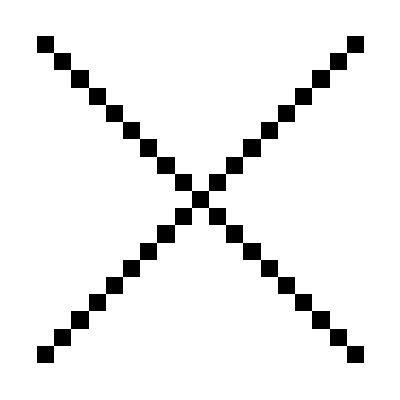

-Graphics-

```mathematica
tempf[m_,mp_,NN_]:=2/NN Chop@NSum[If[n==0,1/2,1]ChebyshevT[n,Cos[(π(m-1/2))/NN]]ChebyshevT[n,Cos[(π(mp-1/2))/NN]],{n,0,NN-1}]
tempf2[m_,mp_,NN_]:=2/NN Chop@NSum[If[n==0,1/2,1]Cos[n ((π(m-1/2))/NN)]Cos[n ((π(mp-1/2))/NN)],{n,0,NN-1}]
tempf2[m_,mp_,NN_]:=2/NN Chop@NSum[If[n==0,1/2,1]Cos[n ((π(m-1/2))/NN)]Cos[n ((π(mp-1/2))/NN)],{n,0,NN-1}]
ArrayPlot@With[{NN=10},Table[tempf[m,mp,NN],{m,Join[Range[-NN+1,-1],Range[1,NN]]},{mp,Join[Range[-NN+1,-1],Range[1,NN]]}]]
ArrayPlot@With[{NN=10},Table[tempf2[m,mp,NN],{m,Join[Range[-NN+1,-1],Range[1,NN]]},{mp,Join[Range[-NN+1,-1],Range[1,NN]]}]]
```

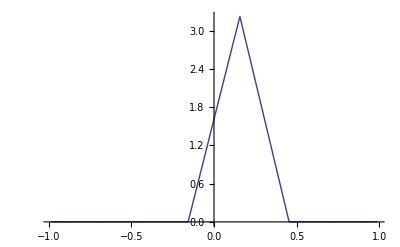

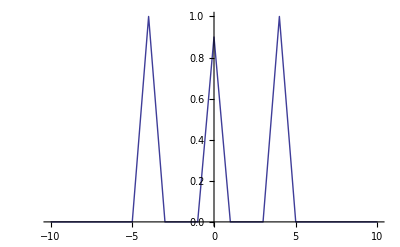

```mathematica
Clear@ChebyVecBare;
ChebyVecBare=Compile[{{ϵ,_Real},{nmax,_Integer}},Prepend[Last/@NestList[{#[[2]],2ϵ #[[2]]-#[[1]]}&,{1,ϵ},nmax-1],1],CompilationTarget->"C", RuntimeAttributes->{Listable}];
ϵmesh[m_,NN_]=Sign[m]Cos[π(m-.5)/NN];
δKCh[m_Integer,mp_Integer,NN_Integer]:=Module[{ϵ=ϵmesh[m,NN],ϵp=ϵmesh[mp,NN],ch1,ch2},ch1=ChebyVecBare[ϵ,NN];ch2=ChebyVecBare[ϵp,NN]; ch1[[1]]*=.5;ch1.ch2 (2/(π √(1-ϵp^2)))]
(*Δ[m_Integer,mp_Integer,NN_Integer]=2Sin[π/(2NN)]Sin[(Abs[m] π)/NN]*)
With[{NN=10,m=-5},{ϵmesh[#,NN],δKCh[#,m,NN]}&/@DeleteCases[Range[-NN,NN],0]];
ListLinePlot[Sort@%, PlotRange->All]
tempf[m_Integer,mp_Integer,NN_Integer]:=2/NN Chop@NSum[If[n==0,1/2,1]ChebyshevT[n,Sign[m]Cos[(π(Abs@m-1/2))/NN]]ChebyshevT[n,Sign[m]Cos[(π(Abs@mp-1/2))/NN]],{n,0,NN-1}]
(*tempf[m_Integer,mp_Integer,NN_Integer]:=2/NN Chop@NSum[If[n==0,1/2,1]ChebyshevT[n,ϵmesh[m,NN]]ChebyshevT[n,ϵmesh[mp,NN]],{n,0,NN-1}]
*)With[{NN=10,m=-4},{#,tempf[#,m,NN]}&/@Range[-NN,NN]];
ListLinePlot[Sort@%, PlotRange->All]
```

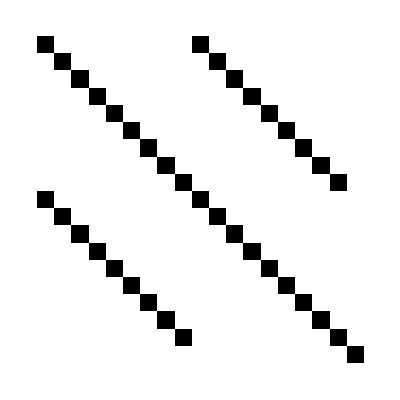

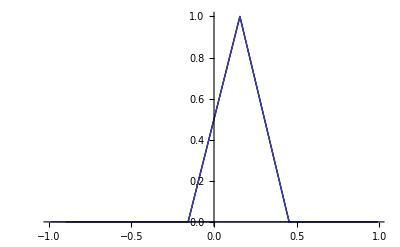

```mathematica
Clear@ChebyVecBare;
ChebyVecBare=Compile[{{ϵ,_Real},{nmax,_Integer}},Prepend[Last/@NestList[{#[[2]],2ϵ #[[2]]-#[[1]]}&,{1,ϵ},nmax-1],1],CompilationTarget->"C", RuntimeAttributes->{Listable}];
ϵmesh[m_,NN_]=Sign[m]Cos[π(m-.5)/NN];
δKCh[m_Integer,mp_Integer,NN_Integer]:=Module[{ϵ=ϵmesh[m,NN],ϵp=ϵmesh[mp,NN],ch1,ch2},ch1=ChebyVecBare[ϵ,NN];ch2=ChebyVecBare[ϵp,NN]; ch1[[1]]*=.5;2/NN ch1.ch2 ]
ArrayPlot@With[{NN=10},Table[Chop@δKCh[m,mp,NN],{m,DeleteCases[Range[-NN+1,NN],0]},{mp,DeleteCases[Range[-NN+1,NN],0]}]]
ListLinePlot[With[{NN=10,m=-5},{ϵmesh[#,NN],δKCh[#,m,NN]}&/@DeleteCases[Range[-NN,NN],0]],PlotRange->All]
```

#### Tests

```mathematica
With[{NN=40,m=31},{ϵmesh[#,NN],tempf2[NN,m,#]}&/@Range[-NN,NN]];
ListLinePlot[%,PlotRange->All]
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

NSum::emcon: Euler-Maclaurin sum failed to converge to requested error tolerance.

General::stop: Further output of NSum :: emcon will be suppressed during this calculation.

$Aborted

ListLinePlot::lpn: $Aborted is not a list of numbers or pairs of numbers.

ListLinePlot[$Aborted,PlotRange→All]

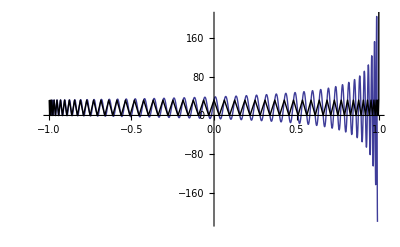

```mathematica
Clear@δCh2;
δCh2[ϵ_?NumericQ,n_Integer]:=(2./(π √(1-ϵ^2)))^-1 ChebyVec[ϵ,n-1].ChebyVec[Cos[π(1)/n],n-1] π/2
With[{n=100},Plot[δCh2[ϵ,n],{ϵ,-.99,.99}, PlotRange->All, Epilog->{Line[{#,δCh2[#,n]}&/@Most@Cos[π(Range[1,n-1])/n]]}]]
```

```mathematica
With[{NN=7,m=2,mp=2},{#,Total@#}&@Table[2./NN Cos[n ((2π)/NN m)]Cos[n ((2π)/NN mp)],{n,0,NN-1}]]
```

{{0.285714,0.0141473,0.231927,0.111068,0.111068,0.231927,0.0141473},1.}

```mathematica
With[{NN=10,m=2,mp=3},1/NN NSum[Exp[-ⅈ n ((2π)/NN m)]Exp[ⅈ n ((2π)/NN mp)],{n,0,NN-1}]]
```

-2.22045×10^-17-4.44089×10^-17 ⅈ

```mathematica
With[{NN=10,m=3,mp=4},NSum[Exp[-ⅈ n ((2π)/NN m)],{n,0,NN-1}]]
```

-2.60902×10^-15+1.33227×10^-15 ⅈ

## DOS

### Mayou DOS

#### Discussion

We wish to compute the DOS,  

	ρ(E)=Tr[δ(E-H)]≈⟨β|δ(E-H)|β⟩, 

where |β⟩ is a normalized random state. (One can also average over several random states to improve accuracy).

We will employ an expansion for the energy projector δ(E-H) in terms of Chebychev polynomials T_n(ϵ), defined in the interval [-1,1]. To this end, we write 

	H=ϵ_0+W h, 

where ϵ_0 and W are c-numbers, and h is an operator with eigenvalues contained in the interval [-1,1]. We will therefore expand  δ (E - H) = 1/W δ((E - ϵ_0)/W- h)=1/W δ(ϵ-h), where ϵ=(E - ϵ_0)/W is the dimensionless Fermi energy, also in the interval [-1,1]. We then have 
We use the spectral resolution of the identity:

	δ(ϵ-ϵ’)=∑_n 1/ν_n N(ϵ) T_n(ϵ)T_n(ϵ'), 

where ν_0=2, ν_(n>0)=1 and N(ϵ)=2/π 1/(√(1-ϵ^2)). The T_n(ϵ) are orthogonal Chebychev polynomials, satsifying 1/ν_n∫_-1^1 dϵ T_n(ϵ)T_m(ϵ) N(ϵ)=δ_nm. The first two are T_0(ϵ)=1 and T_1(ϵ)=ϵ. They satisfy the recurrence

	T_(n+1)(ϵ)=2ϵ T_n(ϵ)-T_(n-1)(ϵ)
	
Using the above, we have a DOS of dimensionless energy ϵ:

	ρ(ϵ)=∑_n N(ϵ) T_n(ϵ)1/ν_n⟨β|T_n(h)|β⟩ 

The “DOS kernel” 1/ν_n⟨β|T_n(h)|β⟩ is computed efficiently by recursion, whereby T_(n+1)(h)|β⟩ =2 h T_n(h)|β⟩-T_(n-1)(h)|β⟩. After each iteration, one projects the resulting state back onto 1/ν_n⟨β|. In this way, only three states are kept in memory at any given time, |β⟩, T_n(h)|β⟩ and T_(n-1)(h)|β⟩.

Low energy projection:
If we wish information about the low energy DOS and the total bandwidth is large, then the resolution W/N might be poor for a reasonable value of N. We may then try to normalize h’=H/W’, where W’ is a smaller energy scale. This in itself doesn’t work, since the whole Chebyshev expasion fails if any eigenvalue of h’ is outside the [-1,1] window. However, we may try to project out the energy components of |β⟩ that lie outside this interval before doing the iterative Chebyshev expansion.
We therefore wish to compute θ(W'^2-H^2)|β⟩=Q|β⟩, where θ is the Heaviside function. We once more use a Chebyshev expansion in h=H/W, so that Q|β⟩=θ(w^2-h^2)|β⟩, where w=W’/W. This time, the expansion reads
	θ(w^2-ϵ^2) =2/(π √(1-w^2))∑_n 1/ν_n T_n(w)μ_n(ϵ)
where μ_n(ϵ)=∫_-1^1 dw θ(w^2-ϵ^2) T_n(w)=∫_-1^1 dw T_n(w)-∫_-ϵ^ϵ dw T_n(w)=[2/(1-n^2)-((T_(n+1)(ϵ))/(n+1)-(T_(n-1)(ϵ))/(n-1))]Cos[(n π)/2]^2. (There is an important caveat here: this only works for ϵ>0, see later).
In an actual calculation, ϵ is substituted by h. The idea is then to compute the states |β_n⟩=T_n(h)|β⟩, and from these, compute
	Q|β⟩=2/(π √(1-w^2))∑_(n=0)^N 1/ν_n Cos[(n π)/2]^2(2/(1-n^2)+(T_(n-1)(h))/(n-1)-(T_(n+1)(h))/(n+1))|β⟩=2/(π √(1-w^2))∑_nm 1/ν_n θ_nm|β_m⟩
The matrix θ_nm(with, n,m=0...N) reads, for n>0,
	1/ν_nθ_nm=(2/(1-n^2)δ_n0+(δ_(n-1,m))/(n-1)-(δ_(n+1,m))/(n+1))Cos[(n π)/2]^2
For n=0, one should actually modify the above to 
	1/ν_0 θ_(0m)= δ_(0m)-δ_(1m)
(using T_-1(ϵ)=T_1(ϵ)=ϵ, and ν_0=2).
A regularizing kernel of coefficients g_n should be included into θ, so we should actually use Θ_nm=g_n θ_nm
Likewise, I should have
	 2/(π √(1-w^2))∑_nm 1/ν_n T_n(w)θ_nm T_m(ϵ)  =θ(w^2-ϵ^2)
since 
	μ_n(ϵ)=∑_m θ_nm T_m(ϵ)

Now the caveat: this expansion only works if ϵ>0. In reality one should write
	 2/(π √(1-w^2))∑_nm 1/ν_n T_n(w)θ_nm T_m(Abs[ϵ])  =θ(w^2-ϵ^2)
Since this is non-polynomical in ϵ, it is useless once we do the replacement ϵ→h. But there is an easy way out. We may write θ(w^2-ϵ^2)=θ(w^4-ϵ^4), so that
	2/(π √(1-w^4))∑_nm 1/ν_n T_n(w^2)θ_nm T_m(ϵ^2)  =θ(w^2-ϵ^2)
so the projector is once more a polynomial of ϵ. This is slightly less efficient than the previous version, but does project out all energies Abs[ϵ]>w+N^(-1/2). The extra N^(-1/2) may be corrected for by writing
	2/(π √(1-(w+1/√N)^4))∑_nm 1/ν_n T_n((w+1/√N)^2)θ_nm T_m(ϵ^2)  =θ(w^2-ϵ^2)

```mathematica
With[{n=6,ϵ=.6},{NIntegrate[ChebyshevT[n,x],{x,-1,-Abs@ϵ}]+NIntegrate[ChebyshevT[n,x],{x,Abs@ϵ,1}],
Cos[(n π)/2]^2(2/(1-n^2)-(ChebyshevT[n+1,ϵ]/(n+1)-ChebyshevT[n-1,ϵ]/(n-1)))}]
```

{-0.212092,-0.212092}

```mathematica
ChebyVec=Compile[{{ϵ,_Real},{nmax,_Integer}},Prepend[Last/@NestList[{#[[2]],2ϵ #[[2]]-#[[1]]}&,{1,ϵ},nmax-1],1],CompilationTarget->"C",RuntimeAttributes->{Listable}];

ThetaJackson[nmax_]:=((((nmax+2-#)Cos[(π#)/(nmax+2)]+Sin[(π#)/(nmax+2)]Cot[π/(nmax+2)])/(nmax+2)&)@Range[0.,nmax])SparseArray[{
{n_,1}:>If[IntegerQ[(n+1)/2],If[n==1,1,2]/(1-(n-1)^2),0],{1,2}->-1,
Band[{3,4}]->(If[IntegerQ[#/2],-1/(#+1),0]&/@Range[2,nmax-1]),
Band[{2,1}]->(If[IntegerQ[#/2],1/(#-1),0]&/@Range[1,nmax])},{nmax+1,nmax+1}]
```

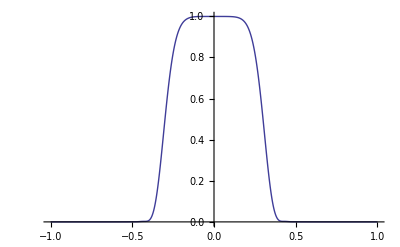

```mathematica
With[{w=0.3,NN=100},
ListLinePlot[2/(π √(1-(w-0 1/(√NN))^4))ChebyVec[(w-0 1/(√NN))^2,NN].ThetaJackson[NN].(ChebyVec[(Range[-1,1,.002])^2,NN]ᵀ), DataRange->{-1,1}, PlotRange->All]]
```

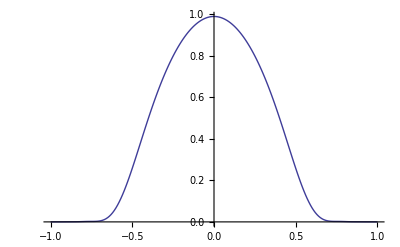

```mathematica
With[{w=0.4,NN=20},
ListLinePlot[2/(π √(1-w^4))ChebyVec[w^2,NN].ThetaJackson[NN].(ChebyVec[(Range[-1,1,.01].99)^2,NN]ᵀ), DataRange->{-1,1}, PlotRange->All]]
```

Looking for a better low energy projector
The essential problem we’re having is that we insist in writing θ(w^2-h^2) as a Chebyshev expansion in w, and hope that the coefficients are combination of Chebyshevs in h. This is the wrong way to go about it. We should expand in h
	θ(w^2-ϵ^2)=∑_n 1/ν_n μ_n(w)T_n(ϵ)
with
	μ_n(w) = ∫_-1^1 (2dϵ)/(π √(1-ϵ^2))T_n(ϵ)θ(w^2-ϵ^2) =∫_-w^w (2dϵ)/(π √(1-ϵ^2))T_n(ϵ) = -2/π ∫_(π-ArcCos[w])^ArcCos[w] dθ Cos[n θ] =4/π Sin[n ArcSin[w]]/n Cos[(n π)/2] 
for n>0. For n=0 we can take the limit, μ_0=4/π ArcSin[w]. As usual, we may regularize the coefficients μ_n with the Jackson kernel, and we may also absorb the 1/ν_n into μ_n.

```mathematica
ChebyVecBare=Compile[{{ϵ,_Real},{nmax,_Integer}},Prepend[Last/@NestList[{#[[2]],2ϵ #[[2]]-#[[1]]}&,{1,ϵ},nmax-1],1],CompilationTarget->"C",RuntimeAttributes->{Listable}];
ThetaJackson[w_,nmax_]:=((((nmax+2-#)Cos[(π#)/(nmax+2)]+Sin[(π#)/(nmax+2)]Cot[π/(nmax+2)])/(nmax+2)&)@Range[0.,nmax])Prepend[4/π Sin[# ArcSin[w]]/# Cos[(# π)/2]&@Range[1,nmax],2/π ArcSin[w]]
```

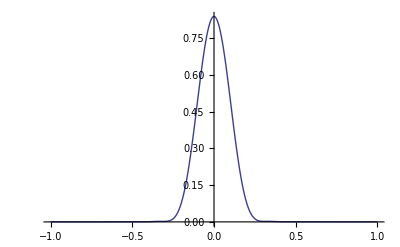

```mathematica
With[{w=0.1,NN=40},
ListLinePlot[(ChebyVecBare[Range[-1,1,.002],NN].ThetaJackson[w,NN]), DataRange->{-1,1}, PlotRange->All]]
```

After testing this idea, the conclusion is that it is not stable: residual high energy components in Q|β⟩ blow up too hard in the Chebyshev expansion

#### Algorithm

```mathematica
Clear@DOSKernel;
Options[DOSKernel]={Samples->1,MaxChebyshev->10, UniformDensity->False, Parallel->False};
DOSKernel[h_SparseArray, opts:OptionsPattern[]]:=
(*DOSKernel[h,opts]=*)Module[{β,hβ,dim=Length@h, kernel,ChebyshevRecursion},

(*If[N@OptionValue@Bandwidth≠1.,h0=H/N@OptionValue@Bandwidth,h0=H];
If[N@OptionValue@BandFraction≠1.,h=h0/(OptionValue@BandFraction+1/√(OptionValue@ProjectorOrder)),h=h0];
h=1.1h0;*)

If[OptionValue@Parallel,ParallelTable,Table][

If[OptionValue@UniformDensity,β=Normalize[Exp[2π ⅈ RandomReal[{0,1},dim]]],β=Normalize[RandomComplex[{-1-ⅈ,1+ⅈ},dim]]];

(*If[N@OptionValue@BandFraction≠1.,
β=Normalize[ThetaJackson[OptionValue@BandFraction,OptionValue@ProjectorOrder].(Prepend[#[[All,2]],#[[1,1]]]&@NestList[{Last@#,2h0.Last@#-First@#}&,{β,h0.β},OptionValue@ProjectorOrder-1])];
];*)

kernel=First@Last@Reap@Nest[{Last@#,((Sow[β*.#];#)&)[2h.Last@#-First@#]}&, ((Sow[β*.#];#)&)/@{β,h.β},OptionValue@MaxChebyshev-1];

kernel[[1]]=0.5;

Re@kernel,{OptionValue@Samples}]
]
```

```mathematica
DOS[kernel_List,OptionsPattern[{ChebyshevMesh->False,NumPoints->Automatic,UseFilter->False,Filter->1/4.{1,2,1}, JacksonKernel->True}]]:=Module[{ϵlist,Npoints,NN=Length@kernel-1, dos},
If[OptionValue@NumPoints===Automatic,Npoints=Length@kernel, Npoints=OptionValue@NumPoints];
If[OptionValue@ChebyshevMesh,ϵlist=ϵmesh[Npoints-1],ϵlist=Most@Rest@Range[-1,1,2/(Npoints+1)]];
If[OptionValue@JacksonKernel,dos=DeltaJackson[ϵlist,NN].kernel,dos=DeltaCheby[ϵlist,NN].kernel];
If[OptionValue@UseFilter,dos=ListConvolve[OptionValue@Filter,dos,1]];
{ϵlist,dos}ᵀ]
```

```mathematica
DeltaCheby=Compile[{{ϵ,_Real},{nmax,_Integer}},2./(π √(1-ϵ^2))Prepend[Last/@NestList[{#[[2]],2ϵ #[[2]]-#[[1]]}&,{1,ϵ},nmax-1],1],CompilationTarget->"C",RuntimeAttributes->{Listable}];

DeltaJackson=Compile[{{ϵ,_Real},{nmax,_Integer}},2./(π √(1-ϵ^2))((((nmax+2-#)Cos[(π#)/(nmax+2)]+Sin[(π#)/(nmax+2)]Cot[π/(nmax+2)])/(nmax+2)&)@Range[0,nmax])Prepend[Last/@NestList[{#[[2]],2ϵ #[[2]]-#[[1]]}&,{1,ϵ},nmax-1],1],CompilationTarget->"C",RuntimeAttributes->{Listable}];

ChebyVec=Compile[{{ϵ,_Real},{nmax,_Integer}},Prepend[Last/@NestList[{#[[2]],2ϵ #[[2]]-#[[1]]}&,{1,ϵ},nmax-1],1],CompilationTarget->"C",RuntimeAttributes->{Listable}];
ThetaJackson[w_,nmax_]:=((((nmax+2-#)Cos[(π#)/(nmax+2)]+Sin[(π#)/(nmax+2)]Cot[π/(nmax+2)])/(nmax+2)&)@Range[0.,nmax])Prepend[4/π Sin[# ArcSin[w]]/# Cos[(# π)/2]&@Range[1,nmax],2/π ArcSin[w]]

ϵmesh[m_,NN_]=Sign[m]Cos[π(m-0.5)/(NN+1)];
ϵmesh[NN_]:=Sort@ϵmesh[Range[1,NN+1],NN]
```

#### Mayou DOS test

```mathematica
DeltaCheby[0.2,10]
```

{0.649747,0.129949,-0.597768,-0.369056,0.450145,0.549114,-0.230499,-0.641314,-0.0260265,0.630904,0.278388}

```mathematica
MeanKernelDOS=Mean@DOSKernel[H[0]/3.01,Samples->1,MaxChebyshev->300, Parallel->False, BandFraction->1, ProjectorOrder->20];//AbsoluteTiming
```

OptionValue::nodef: Unknown option "BandFraction" for DOSKernel.

OptionValue::nodef: Unknown option "ProjectorOrder" for DOSKernel.

OptionValue::nodef: Unknown option "BandFraction" for DOSKernel.

General::stop: Further output of OptionValue :: nodef will be suppressed during this calculation.

{5.522243,Null}

```mathematica
{5.101168`7.159214620158218,Null}
```

{5.101168,Null}

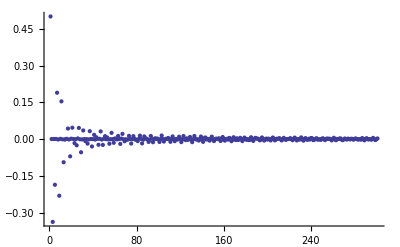

```mathematica
ListPlot@MeanKernelDOS
```

```mathematica
SetDirectory@NotebookDirectory[];
<<"./DOSKernel-1024-1024-1.dat";
```

```mathematica
ListLinePlot[DOS[MeanKernelDOS], PlotRange->{-1,1}.001]
```

-Graphics-

```mathematica
DOS[MeanKernelDOS][[1]]
```

{-150/151,0.415479}

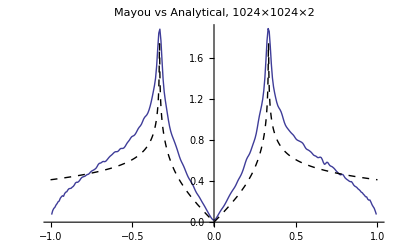

```mathematica
ListLinePlot[DOS[MeanKernelDOS], PlotRange->All];
Show[%,Plot[3/2 AnalyticDOS[3ϵ],{ϵ,-1,1},PlotStyle->{{Black,Dashed}}, PlotRange->All],PlotLabel->"Mayou vs Analytical, 1024×1024×2"]
```

## Conductivity

### Mayou’s Kubo algorithm

#### Discussion

We compute the Kubo dc conductivity σ_xx(ω), which is an integral 

	Re σ_xx(ω)=(2 e^2 ℏ)/Ω∫dE (f(E)-f(E+ℏω))/ℏω F(E,E')

of 

	F(E,E’) = Tr[V_x δ(E-H) V_x δ(E’-H)] ≈N/S∑_(p=1)^S ⟨β_p| V_x δ(E-H) V_x δ(E’-H) |β_p⟩, 

where V_x=-ⅈ[H,X] is the x-velocity, X is the x-position operator, H is the Hamiltonian, of size NxN, E is the Fermi energy, and |β_p⟩ are (normalized) random states (in large systems using only a single state [S=1] is enough).  This can be trivially generalized to Re σ_xy.

We will employ an expansion for the energy projectors δ(E-H) in terms of Chebychev polynomials T_n(ϵ), defined in the interval [-1,1]. To this end, we write 

	H=ϵ_0+W h, 
	
where ϵ_0 and W are c-numbers, and h is an operator with eigenvalues contained in the interval [-1,1]. We will therefore expand  δ (E - H) = 1/W δ((E - ϵ_0)/W- h)=1/W δ(ϵ-h), where ϵ=(E - ϵ_0)/W is the dimensionless Fermi energy, also in the interval [-1,1]. We then have 

	F(ϵ,ϵ') = ⟨β| v_x δ(ϵ-h) v_x δ(ϵ’-h) |β⟩  

where v_x=-ⅈ[h,X]=V_x/W. (The W factors cancel).

We use the spectral resolution of the identity:

	δ(ϵ-ϵ’)=∑_n 1/ν_n N(ϵ) T_n(ϵ)T_n(ϵ'), 
	
where ν_0=2, ν_(n>0)=1 and N(ϵ)=2/π 1/(√(1-ϵ^2)). The T_n(ϵ) are orthogonal Chebychev polynomials, satsifying 1/ν_n∫_-1^1 dϵ T_n(ϵ)T_m(ϵ) N(ϵ)=δ_nm. The first two are T_0(ϵ)=1 and T_1(ϵ)=ϵ. They satisfy the recurrence

	T_(n+1)(ϵ)=2ϵ T_n(ϵ)-T_(n-1)(ϵ)
	
Using the above, we can write F(ϵ,ϵ’) 

	F (ϵ, ϵ') = ∑_nm 1/(ν_n ν_m)⟨β|v_x T_n(h)v_x T_m(h)|β⟩T_n(ϵ) T_m(ϵ')

in terms of the “Kubo Kernel” 1/(ν_n ν_m)⟨β|v_x T_n(h)v_x T_m(h)|β⟩

A practical way to compute the Kubo Kernel is a two step recursion, whereby we first compute (and store) the bras 1/(ν_n ν_m)⟨β|v_x T_n(h)v_x, (for n=0,... nmax) using T_m(h) recursion, and then do a second recursion for T_m(h)|β⟩, in which we only store two states at any given time, like for the DOS. In the second recursion cycle we project onto the 1/(ν_n ν_m)⟨β|v_x T_n(h)v_x bras at each step, “sowing” the results along the way, which are “reaped” only at the end for numerical efficiency.

Regarding the exact coefficient of σ, Kubo says:

	σ(ω)=-ⅈ g(e^2 ℏ)/(ℏω A)∑_nm (f(E_m)-f(E_n))/(ℏω-E_m+E_n+ⅈ0)⟨m|v|n⟩⟨n|v|m⟩
	Re[σ(ω)]=g(π e^2 ℏ)/A∑_nm (f(E_m)-f(E_n))/(ℏ ω)δ(ℏω-E_m+E_n)⟨m|v|n⟩⟨n|v|m⟩ =g(π e^2 ℏ)/A∫dE (f(E)-f(E+ℏω))/(ℏ ω)Tr[v δ(E-H) v δ(E+ℏω-H)]=g(π e^2 ℏ)/(W^2 A/N)∫dϵ (f(ϵ)-f(ϵ+ℏω/W))/(ℏ ω/W)F(ϵ,ϵ+ℏω/W)=g (π e^2 ℏ)/(W^2 A/N)∫dϵ (f(ϵ)-f(ϵ+ℏω/W))/(ℏ ω/W)F(ϵ,ϵ+ℏω/W)=(2 π^2 g ℏ^2)/(W^2 A/N) e^2/h∫dϵ (f(ϵ)-f(ϵ+ℏω/W))/(ℏ ω/W)F(ϵ,ϵ+ℏω/W)
	
Here, g is the degeneracy of each normalized state |n⟩ (often g=g_s=2), while A is the area of the system, and A/N is the area per site of the lattice. In the last expression, Fermi functions are evaluated for dimensionless temperature K_B t=K_B T/W

Optimal meshing of integrals
We recall that, for an expansion of order N, the optimal energy mesh should be the zeroes of T_(N+1). This gives the best resolution of the Delta function.
When evalating σ, we should actually compute F(ϵ_m,ϵ_m'). The integral would then be computed as a sum. The problem with this approach is that if ϵ_m belongs to the optimal mesh, then ϵ_m+ℏω/W will not. An option is the use the mesh to build an interpolation function F(ϵ,ϵ’) for all ϵ, ϵ’. In this case, linear interpolation will work best, since there will be zero overshoot in delta-like features

#### Algorithm

```mathematica
Clear@KuboKernel;
Options[KuboKernel]={Samples->1,MaxChebyshev->100, UniformDensity->True, Parallel->False};
KuboKernel[h_SparseArray,v_SparseArray, opts:OptionsPattern[]]:=
KuboKernel[h,v, opts]=Module[{β,βv,βvTv, dim=Length@h, w,ChebyshevRecursion},

(*ChebyshevRecursion[{βa_, βb_}]:={βb,2h.βb-βa};*)

If[OptionValue@Parallel,ParallelTable,Table][
Clear[βvTv,βv,β,w];
If[OptionValue@UniformDensity,β=Normalize[Exp[2π ⅈ RandomReal[{0,1},dim]]],β=Normalize[RandomComplex[{-1-ⅈ,1+ⅈ},dim]]];

βv=β*.v;

(*βvTv=(First@Last@Reap@(Nest[{Last@#,(Sow[#.v];#)&[2Last@#.h-First@#]}&,(Sow[#.v];#)&/@{βv,βv.h},OptionValue@MaxChebyshev-1];))*);
(*βvTv=(Prepend[Last[#].v&/@NestList[{Last@#,2Last@#.h-First@#}&,{βv,βv.h},OptionValue@MaxChebyshev-1],βv.v])*);
(*βvTv=(First@Last@Reap@(Nest[{Last@#,(Sow[#.v];#)&[2Last@#.h-First@#]}&,(Sow[#.v];#)&/@{βv,βv.h},OptionValue@MaxChebyshev-1];));*)
(*βvTv=(Prepend[Last/@NestList[{Last@#,2Last@#.h-First@#}&,{βv,βv.h},OptionValue@MaxChebyshev-1],βv].v)*);

βvTv=(First@Last@Reap@(Nest[{Last@#,Sow[2Last@#.h-First@#]}&,Sow/@{βv,βv.h},OptionValue@MaxChebyshev-1];).v);

w=First@Last@Reap@(Nest[{Last@#,(Sow[βvTv.#];#)&[2h.Last@#-First@#]}&,(Sow[βvTv.#];#)&/@{β,h.β},OptionValue@MaxChebyshev-1];); 
(*w=Join[{βvTv.β},#[[2,1]],{βvTv.#[[1,2]]}]&@Reap@Nest[ChebyshevRecursion[Sow[βvTv.Last@#];#]&,{β,h.β},OptionValue@MaxChebyshev-1]*);

w[[All,1]]*=0.5;w[[1,All]]*=0.5;(*This includes the weight Subscript[ν, n] into the polynomials Subscript[T, n][h]*)
Re@((w+w†)/2),{OptionValue@Samples}] (*The Re@(w+w†)/2 enforcement is unnecessary when averaging over many β (trace property)*)
]
```

```mathematica
Clear@ChebyVec;
ChebyVec=Compile[{{ϵ,_Real},{nmax,_Integer}},2./(π √(1-ϵ^2))Prepend[Last/@NestList[{#[[2]],2ϵ #[[2]]-#[[1]]}&,{1,ϵ},nmax-1],1],CompilationTarget->"C",RuntimeAttributes->{Listable}];
DeltaJackson=Compile[{{ϵ,_Real},{nmax,_Integer}},2./(π √(1-ϵ^2))((((nmax+2-#)Cos[(π#)/(nmax+2)]+Sin[(π#)/(nmax+2)]Cot[π/(nmax+2)])/(nmax+2)&)@Range[0,nmax])Prepend[Last/@NestList[{#[[2]],2ϵ #[[2]]-#[[1]]}&,{1,ϵ},nmax-1],1],CompilationTarget->"C",RuntimeAttributes->{Listable}];

ϵmesh[m_,NN_]=Sign[m]Cos[π(m-0.5)/(NN+1)];
ϵmesh[NN_]:=Sort@ϵmesh[Range[1,NN+1],NN]
(*ϵmesh[NN_]:=.99Sort@Range[-1,1,1/Round[NN/π]]*)

KuboσF[kernel_List, OptionsPattern[{ChebyshevMesh->False,NumPoints->Automatic,UseFilter->False,Filter->1/8.({{0, 1, 0}, {1, 4, 1}, {0, 1, 0}}), JacksonKernel->True,InterpolationOrder->1}]]:=Module[{ϵlist,delta,NN=Length@kernel-1,Npoints,F,ϵϵ, data},
If[OptionValue@NumPoints===Automatic,Npoints=Length@kernel, Npoints=OptionValue@NumPoints];
If[OptionValue@ChebyshevMesh,ϵlist=ϵmesh[Npoints-1],ϵlist=Most@Rest@Range[-1,1,2/(Npoints+1)]];
If[OptionValue@JacksonKernel,delta=DeltaJackson[ϵlist, NN],delta=ChebyVec[ϵlist, NN]];
F=delta.kernel.deltaᵀ;
(*If[OptionValue@SuppressDrudePeak,Table[F[[i,i]]=0.,{i,1,Length[F]}]];*)
If[OptionValue@UseFilter,F=ListConvolve[OptionValue@Filter,F,1]];
ϵϵ=Outer[List,ϵlist,ϵlist];
data=MapThread[Append,{ϵϵ,F},2];
temp=data[[All,All,3]];
Interpolation[Flatten[data,1], InterpolationOrder->OptionValue@InterpolationOrder]];
```

#### Experimental Kernel

```mathematica
Clear@KuboKernelExp;
Options[KuboKernelExp]={Samples->1,Samples2->1,MaxChebyshev->100,  Parallel->False};
KuboKernelExp[h_SparseArray,v_SparseArray, opts:OptionsPattern[]]:=
Module[{β,β1,βv,βvTvβ1,β1Tβ, dim=Length@h, w,ChebyshevRecursion},

(*ChebyshevRecursion[{βa_, βb_}]:={βb,2h.βb-βa};*)

Flatten[#,1]&@If[OptionValue@Parallel,ParallelTable,Table][
Clear[βv,β];
β=Normalize[Exp[2π ⅈ RandomReal[{0,1},dim]]];βv=β*.v;

Table[
Clear[βvTvβ1,β1Tβ,w];
β1=Normalize[Exp[2π ⅈ RandomReal[{0,1},dim]]];

(*βvTv=(First@Last@Reap@(Nest[{Last@#,(Sow[#.v];#)&[2Last@#.h-First@#]}&,(Sow[#.v];#)&/@{βv,βv.h},OptionValue@MaxChebyshev-1];))*);
(*βvTv=(Prepend[Last[#].v&/@NestList[{Last@#,2Last@#.h-First@#}&,{βv,βv.h},OptionValue@MaxChebyshev-1],βv.v])*);
(*βvTv=(First@Last@Reap@(Nest[{Last@#,(Sow[#.v];#)&[2Last@#.h-First@#]}&,(Sow[#.v];#)&/@{βv,βv.h},OptionValue@MaxChebyshev-1];));*)
(*βvTv=(Prepend[Last/@NestList[{Last@#,2Last@#.h-First@#}&,{βv,βv.h},OptionValue@MaxChebyshev-1],βv].v)*);

βvTvβ1=(First@Last@Reap@(Nest[{Last@#,(Sow[#.v.β1];#)&[2Last@#.h-First@#]}&,((Sow[#.v.β1];#)&)/@{βv,βv.h},OptionValue@MaxChebyshev-1];));
β1=β1*;
β1Tβ=(First@Last@Reap@(Nest[{Last@#,(Sow[β1.#];#)&[2h.Last@#-First@#]}&,((Sow[β1.#];#)&)/@{β,h.β},OptionValue@MaxChebyshev-1];));

w=dim Outer[Times,βvTvβ1, β1Tβ]; 
(*w=Join[{βvTv.β},#[[2,1]],{βvTv.#[[1,2]]}]&@Reap@Nest[ChebyshevRecursion[Sow[βvTv.Last@#];#]&,{β,h.β},OptionValue@MaxChebyshev-1]*);

w[[All,1]]*=0.5;w[[1,All]]*=0.5;(*This includes the weight Subscript[ν, n] into the polynomials Subscript[T, n][h]*)
Re@((w+w†)/2),{OptionValue@Samples2}],{OptionValue@Samples}] (*The Re@(w+w†)/2 enforcement is unnecessary when averaging over many β (trace property)*)
]
```

```mathematica
Clear@KuboKernelExp;
Options[KuboKernelExp]={Samples->1,MaxChebyshev->100,  Parallel->False};
KuboKernelExp[h_SparseArray,v_SparseArray, opts:OptionsPattern[]]:=
Module[{β,β1,βv,βvTvβ1,β1Tβ, dim=Length@h, w,counter},

If[OptionValue@Parallel,ParallelTable,Table][
Print[counter];
Clear[βv,β];
β=Normalize[Exp[2π ⅈ RandomReal[{0,1},dim]]];βv=β*.v;

Clear[βvTvβ1,β1Tβ,w];
β1=Normalize[Exp[2π ⅈ RandomReal[{0,1},dim]]];

(*βvTv=(First@Last@Reap@(Nest[{Last@#,(Sow[#.v];#)&[2Last@#.h-First@#]}&,(Sow[#.v];#)&/@{βv,βv.h},OptionValue@MaxChebyshev-1];))*);
(*βvTv=(Prepend[Last[#].v&/@NestList[{Last@#,2Last@#.h-First@#}&,{βv,βv.h},OptionValue@MaxChebyshev-1],βv.v])*);
(*βvTv=(First@Last@Reap@(Nest[{Last@#,(Sow[#.v];#)&[2Last@#.h-First@#]}&,(Sow[#.v];#)&/@{βv,βv.h},OptionValue@MaxChebyshev-1];));*)
(*βvTv=(Prepend[Last/@NestList[{Last@#,2Last@#.h-First@#}&,{βv,βv.h},OptionValue@MaxChebyshev-1],βv].v)*);

βvTvβ1=(First@Last@Reap@(Nest[{Last@#,(Sow[#.v.β1];#)&[2Last@#.h-First@#]}&,((Sow[#.v.β1];#)&)/@{βv,βv.h},OptionValue@MaxChebyshev-1];));
β1=β1*;
β1Tβ=(First@Last@Reap@(Nest[{Last@#,(Sow[β1.#];#)&[2h.Last@#-First@#]}&,((Sow[β1.#];#)&)/@{β,h.β},OptionValue@MaxChebyshev-1];));

w=dim Outer[Times,βvTvβ1, β1Tβ]; 
(*w=Join[{βvTv.β},#[[2,1]],{βvTv.#[[1,2]]}]&@Reap@Nest[ChebyshevRecursion[Sow[βvTv.Last@#];#]&,{β,h.β},OptionValue@MaxChebyshev-1]*);

w[[All,1]]*=0.5;w[[1,All]]*=0.5;(*This includes the weight Subscript[ν, n] into the polynomials Subscript[T, n][h]*)
Re@((w+w†)/2),{counter,1,OptionValue@Samples}] (*The Re@(w+w†)/2 enforcement is unnecessary when averaging over many β (trace property)*)

]
```

### Tests

#### Mayou Kubo Tests

```mathematica
CloseKernels[];LaunchKernels[3];
```

```mathematica
tempK=KuboKernel[H[0]/3,vx/1.5,MaxChebyshev->nmax, Samples->64, Parallel->False];//AbsoluteTiming
(*ArrayPlot[tempK, PlotRange->All]*)
```

{1.61045,Null}

```mathematica
SetDirectory@NotebookDirectory[];
<<"../KuboKernel-600-600-64.dat";
tempK600=tempK;
nmax=600;
```

```mathematica
SetDirectory@NotebookDirectory[];
<<"../KuboKernel-300-300-64.dat";
tempK300=tempK;
nmax=300;
```

```mathematica
MeanKernel=Mean@tempK300;
Dimensions@%
```

{301,301}

```mathematica
Clear@tempi
tempi=KuboσF[MeanKernel,JacksonKernel->False,ChebyshevMesh->True,UseFilter->True,InterpolationOrder->1]
f[ω_]:=1/(1+ⅇ^ω)
Clear@σ;
σ[ϵF_, ω_, T_:0.000001]:=(2π)^2/((3 √3)/2/2)1.5^2/3^2 NIntegrate[(f[(ϵ-ϵF)/T]-f[(ϵ-ϵF+ω)/T])/ω tempi[ϵ,ϵ+ω],{ϵ,ϵF-Max[ω,0]-3T,ϵF+Max[-ω,0]+3T}]
```

InterpolatingFunction[{{-0.999986,0.999986},{-0.999986,0.999986}},<>]

```mathematica
Clear@tempi
tempi=KuboσF[MeanKernel]
f[ω_]:=1/(1+ⅇ^ω)
Clear@σ;
σ[ϵF_, ω_, T_:0.000001]:=(2π)^2/((3 √3)/2/2)1.5^2/3^2 NIntegrate[(f[(ϵ-ϵF)/T]-f[(ϵ-ϵF+ω)/T])/ω tempi[ϵ,ϵ+ω],{ϵ,ϵF-Max[ω,0]-3T,ϵF+Max[-ω,0]+3T}]
```

InterpolatingFunction[{{-0.993377,0.993377},{-0.993377,0.993377}},<>]

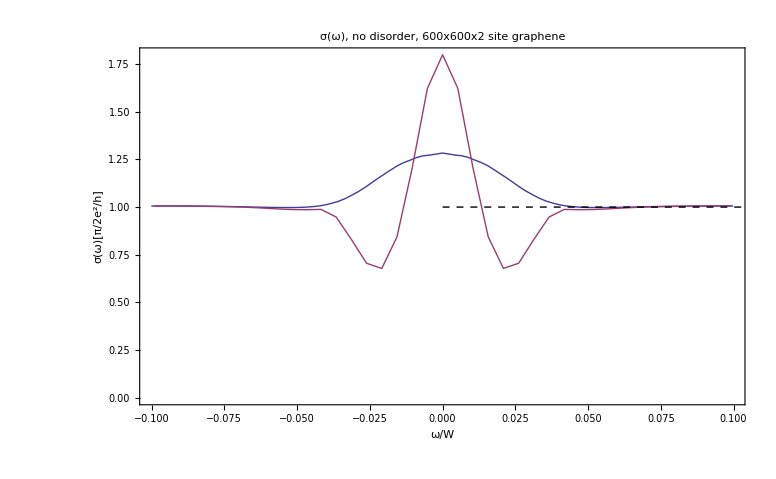

```mathematica
tempp=Parallelize[{#,2/π σ[0.,#]}&/@Range[-.1001,.1,(.2)/90]]; 
ListLinePlot[{tempp,temppold}, PlotRange->{0,All},PlotRange->All, PlotRangePadding->None, Frame->True, FrameLabel->{"ω/W","σ(ω)[π/2e^2/h]"},BaseStyle->FontSize->15,PlotLabel->"σ(ω), no disorder, 600x600x2 site graphene", Epilog->{Dashed,Line[{{0,#},{1,#}}&@1]}]
```

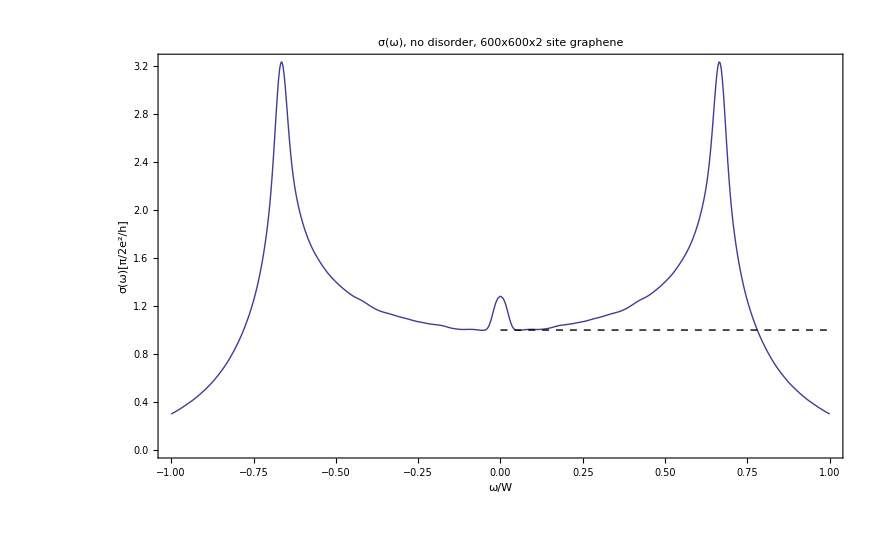

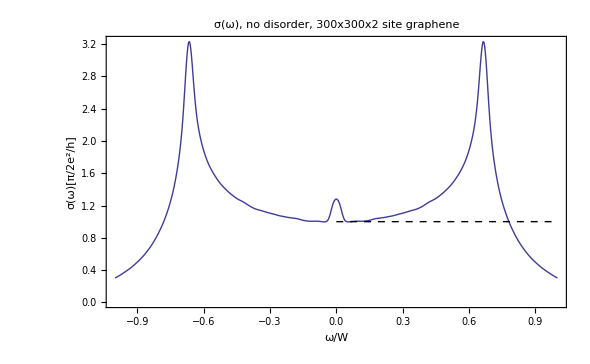

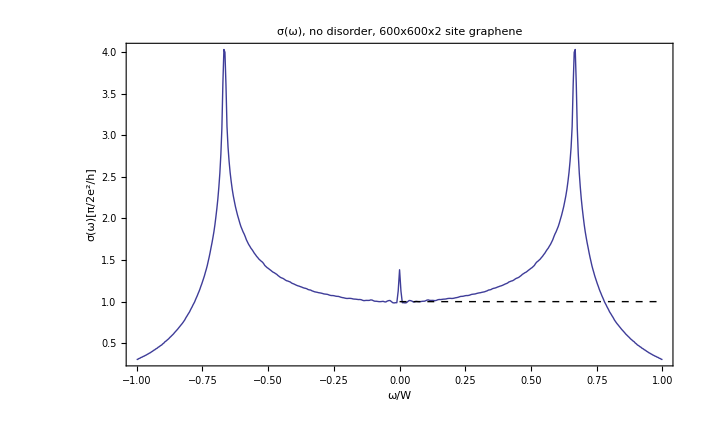

```mathematica
tempp=Parallelize[{#,2/π σ[0.,#]}&/@Range[-1,1,2./601]]; 
ListLinePlot[tempp, PlotRange->{0,All},PlotRange->All, PlotRangePadding->None, Frame->True, FrameLabel->{"ω/W","σ(ω)[π/2e^2/h]"},BaseStyle->FontSize->15,PlotLabel->"σ(ω), no disorder, 600x600x2 site graphene", Epilog->{Dashed,Line[{{0,#},{1,#}}&@1]}]
```

#### PETSC kernel Tests

```mathematica
SetDirectory@NotebookDirectory[];
MeanKernel0=Import["dat_MkII_8_part.dat"];
MeanKernel=Partition[MeanKernel0[[All,1]]+ⅈ MeanKernel0[[All,2]],600];
```

```mathematica
Partition[MeanKernel0[[All,2]],600];
Max@Abs[%-%ᵀ]
```

6.95245×10^-18

```mathematica
SetDirectory@NotebookDirectory[];
MeanKernel=Import["DAT_64_averaged.dat"];
```

```mathematica
SetDirectory@NotebookDirectory[];
MeanKernel0=Import["DAT_new2.dat"];
MeanKernel=Partition[MeanKernel0[[All,1]],600];
```

```mathematica
SetDirectory@NotebookDirectory[];
<<"../KuboKernel-600-600-64.dat";
MeanKernel2=Mean@tempK;
```

```mathematica
ArrayPlot[Log@MeanKernel2]
```

-Graphics-

```mathematica
ArrayPlot[Log@MeanKernel]
```

-Graphics-

```mathematica
Clear@tempi
tempi=KuboσF[MeanKernel]
f[ω_]:=1/(1+ⅇ^ω)
Clear@σ;
σ[ϵF_, ω_, T_:0.000001]:=(2π)^2/((3 √3)/2/2)3.1^2/3.1^2 NIntegrate[(f[(ϵ-ϵF)/T]-f[(ϵ-ϵF+ω)/T])/ω tempi[ϵ,ϵ+ω],{ϵ,ϵF-Max[ω,0]-3T,ϵF+Max[-ω,0]+3T}]
```

InterpolatingFunction[{{-0.996672,0.996672},{-0.996672,0.996672}},<>]

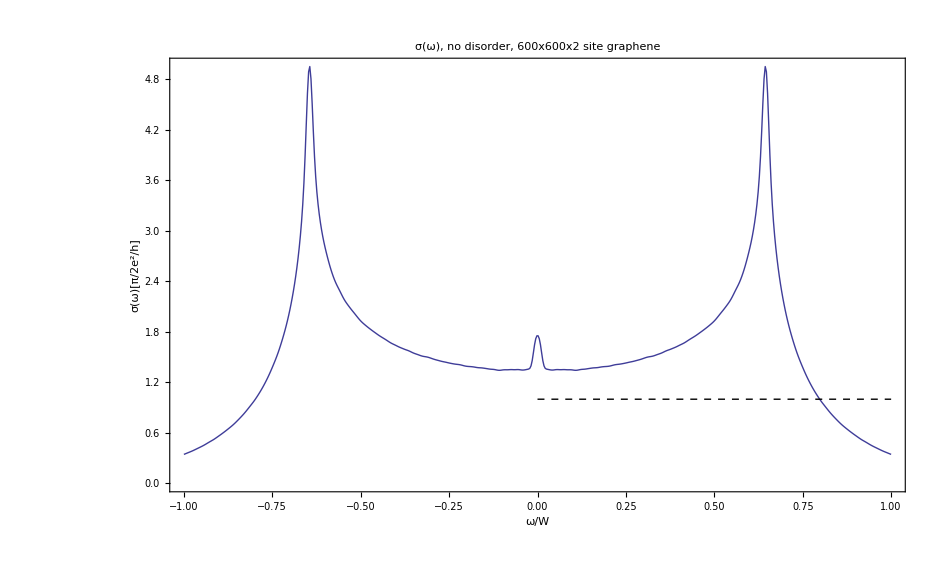

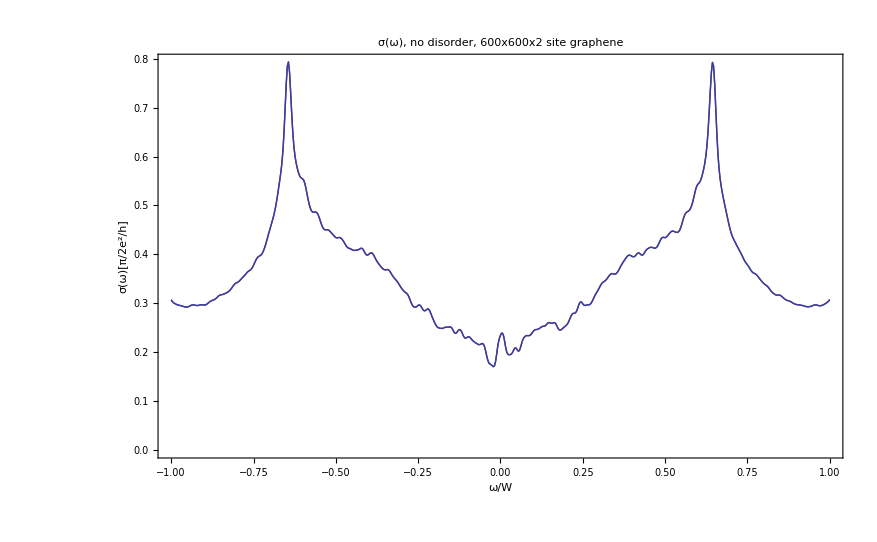

```mathematica
tempp=Parallelize[{#,2/π σ[0.,#]}&/@Range[-1,1,2./601]]; 
ListLinePlot[tempp, PlotRange->{0,All},PlotRange->All, PlotRangePadding->None, Frame->True, FrameLabel->{"ω/W","σ(ω)[π/2e^2/h]"},BaseStyle->FontSize->15,PlotLabel->"σ(ω), no disorder, 600x600x2 site graphene", Epilog->{Dashed,Line[{{0,#},{1,#}}&@1]}]
```

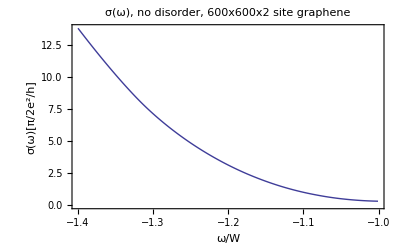

-Graphics-

-Graphics-

```mathematica
tempp=Parallelize[{#,2/π σ[0.,#]}&/@Range[-1.4,-1,2./601]]; 
ListLinePlot[tempp, PlotRange->{0,All},PlotRange->All, PlotRangePadding->None, Frame->True, FrameLabel->{"ω/W","σ(ω)[π/2e^2/h]"},BaseStyle->FontSize->15,PlotLabel->"σ(ω), no disorder, 600x600x2 site graphene", Epilog->{Dashed,Line[{{0,#},{1,#}}&@1]}]
```

#### Test for László

```mathematica
CloseKernels[];LaunchKernels[3];
```

```mathematica
tempK=Mean@KuboKernel[H[0]/3,vx,MaxChebyshev->300, Samples->1, Parallel->False];//AbsoluteTiming
(*ArrayPlot[tempK, PlotRange->All]*)
```

{52.80218,Null}

{52.90743,Null}

```mathematica
tempKexp=Mean@KuboKernelExp[H[0]/3,vx,MaxChebyshev->300, Samples->8,Samples2->8, Parallel->True];//AbsoluteTiming
```

{140.65627,Null}

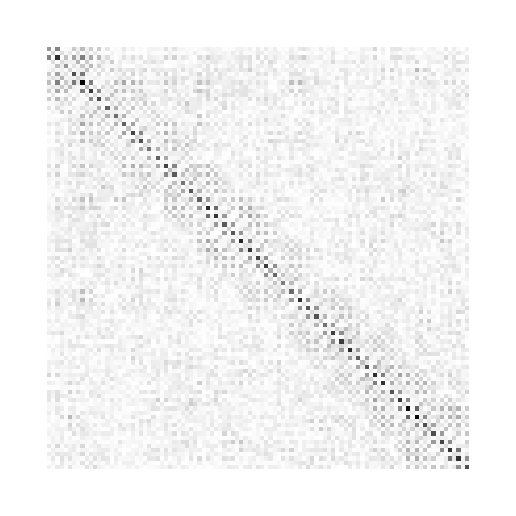

```mathematica
ArrayPlot[tempKexp]
```

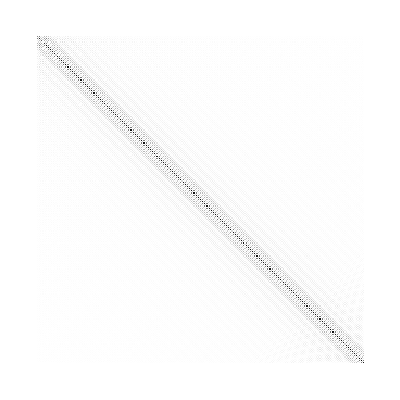

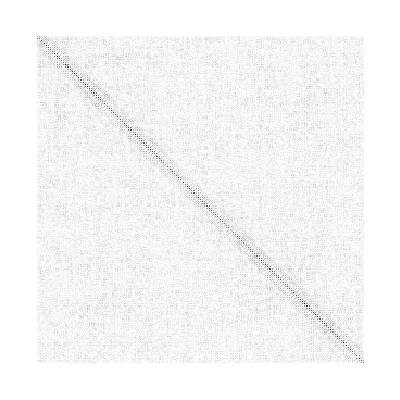

```mathematica
ArrayPlot[tempK]
ArrayPlot[tempKexp]
```

```mathematica
Clear@tempi
tempi=KuboσF[tempKexp]
f[ω_]:=1/(1+ⅇ^ω)
Clear@σ;
σ[ϵF_, ω_, T_:0.000001]:=(2π)^2/((3 √3)/2/2)1/3.1^2 NIntegrate[(f[(ϵ-ϵF)/T]-f[(ϵ-ϵF+ω)/T])/ω tempi[ϵ,ϵ+ω],{ϵ,ϵF-Max[ω,0]-3T,ϵF+Max[-ω,0]+3T}]
```

InterpolatingFunction[{{-0.993377,0.993377},{-0.993377,0.993377}},<>]

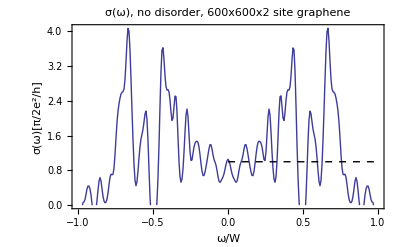

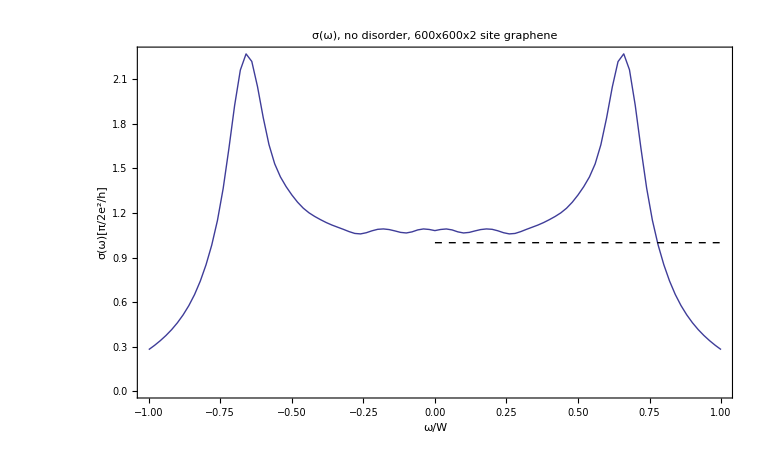

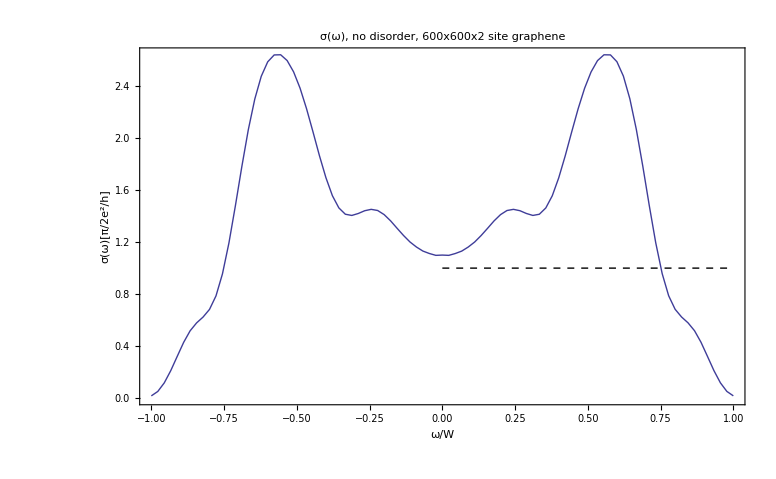

```mathematica
tempp=Parallelize[{#,2/π σ[0.,#]}&/@Range[-1.0001,1,2./300]]; 
ListLinePlot[tempp, PlotRange->{0,All},PlotRange->All, PlotRangePadding->None, Frame->True, FrameLabel->{"ω/W","σ(ω)[π/2e^2/h]"},BaseStyle->FontSize->15,PlotLabel->"σ(ω), no disorder, 600x600x2 site graphene", Epilog->{Dashed,Line[{{0,#},{1,#}}&@1]}]
```

```mathematica
SetDirectory@NotebookDirectory[];
Export["NormalizedHamiltonian-50x50x2.mtx",H[0]/3]
```

$Aborted